## Star - Disk magnetic field interaction

### Setup

```mathematica
$HistoryLength=0;ClearAll["Global`*"]; 
SetDirectory["/home/dagl4841/ResearchLocal/netFieldEvo/mathematica"];
```

```mathematica
rloglog[functions_,yLabel_,legendLabels_,coords_]:=LogLogPlot[functions, {r,rMin,rMax}, Frame->True,FrameLabel->{"r (AU)", yLabel},ImageSize->Large,PlotLegends->legendLabels,BaseStyle->{FontWeight->"Bold",FontSize->14},PlotRange->Full, GridLines->coords]
au=1.5*10^13;
G=6.67*10^-8;
Msun=2*10^33;
Mstar=1.0*Msun;
mp=1*10^-24;
kb=1.38*10^-16;
year=3.15*10^7;
σ = 5.67*10^-5;
rMin=r0star;
rMax=10;
```

### Stellar field

```mathematica
r0star=0.01; (* 1/200 of an AU is roughly photosphere *)
```

### MMSN model

```mathematica
(* input r is in au, other quantities are in cm *)
r0disk=1;
μ=2.7;
Σ[r_]:=1700 * (r/r0disk)^(-3/2); 
T[r_]:=280*(r/r0disk)^(-1/2)
cs[r_]:=√((kb T[r])/(μ mp)) ;
Ω[r_]:=√((G Mstar)/(r*au)^3)
h[r_]:=cs[r]/Ω[r];
hor[r_]:=h[r]/(r*au)
ρ[r_]:=1/(√(2π))Σ[r]/h[r];
P[r_]:=ρ[r]*cs[r]^2;
```

```mathematica
rDZ=Solve[T[r]==800,r][[1,1,2]]//N
```

0.1225

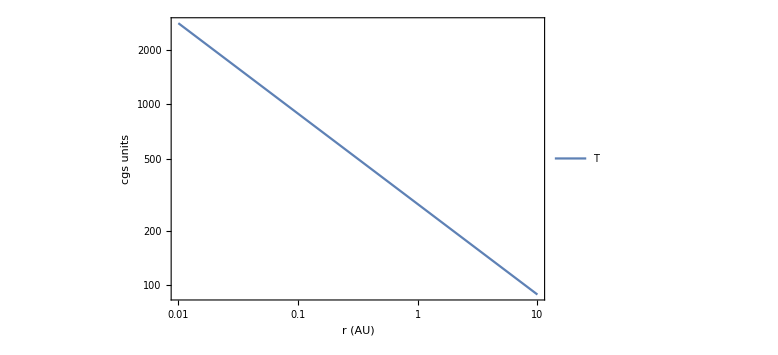

```mathematica
rloglog[{T[r]}, "cgs units",{"T"},{{rDZ},{800}}]
```

### Chiang-Goldreich model (valid between 0.4 au and 84 au), from phil’s text p. 50

```mathematica
(* input r is in au, other quantities are in cm *)
μ=2.7;
Tcg[r_]:=150*(r/1)^(-3/7)
```

### Active Disk (phil’s text p. 75). also see Garaud and Lin 2007

```mathematica
(* input r is in au, other quantities are in cm *)
(*Td[r_,Mdot_]:=((3G Msun Mdot*Msun/year)/(8 π σ (r*au)^3)(1-√((r0star*au)/(r*au))))^(1/4)
Tc[r_,Mdot_]:=(3/4 τ[r] )^(1/4)Td[r,Mdot]
τ[r_]:=1/2 Σ[r]κR[r]
κR[r_]:=0.1*)
```

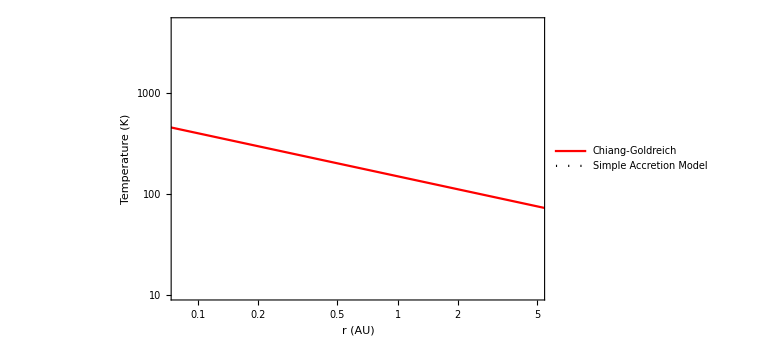

TemperatureProfiles.png

```mathematica
plt=LogLogPlot[
{Tcg[r],Tc[r,10^-6],Tc[r,10^-7],Tc[r,10^-8],Tc[r,10^-9],Tc[r,10^-10]}, {r,rMin,rMax},
 Frame->True,FrameLabel->{"r (AU)", "Temperature (K)"},
ImageSize->Large,
PlotLegends->Placed[{"Chiang-Goldreich","Simple Accretion Model"},{0.75,0.87}],
BaseStyle->{FontWeight->"Normal",FontSize->14},
PlotRange->{{0.08,5},{10,5000}},
 GridLines->{{},{800}}, 
GridLinesStyle->{{Gray},{Gray}},
PlotStyle->{{Red},{Black, Dotted},{Black, Dotted},{Black, Dotted},{Black, Dotted},{Black, Dotted},{Black, Dotted}}
]
Export["TemperatureProfiles.png",plt]
```

```mathematica
Td1[r_,Mdot_]:=((3G Msun Mdot*Msun/year)/(8 π σ (r*au)^3))^(1/4);
```

```mathematica
eqTab[r_,Mdot_]:={
Tc1==(3/4 τ )^(1/4)Td1[r,Mdot],
τ==1/2 Σ[r]κR,
κR==If[Tc1>1000,0.003,If[Tc1<125,Tc1^2*0.0002,3]],
Tc1>0
}
```